```mathematica
CoprimeQ[Range[1000000], 1000000] // Short
```

{True,False,True,False,False,False,«999989»,False,True,False,True,False}

```mathematica
% /. False -> Nothing // Short
```

{True,True,True,True,True,True,«399988»,True,True,True,True,True,True}

```mathematica
Length[%]
```

400000

```mathematica
Length[CoprimeQ[Range[1000000], 1000000] /. False -> Nothing]
```

400000

```mathematica
∑_(i=1)^n i^2
```

1/6 n (1+n) (1+2 n)

```mathematica
∑_(i=1)^n i^k
```

HarmonicNumber[n,-k]

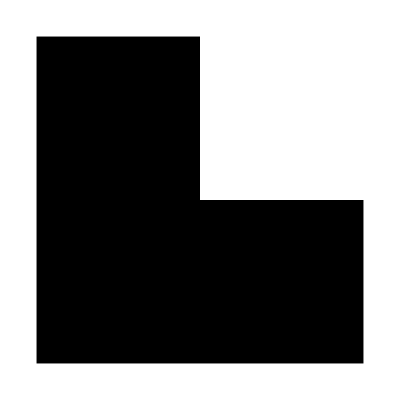
-Graphics-n

```mathematica
Labeled[Graphics[
  shape = {Rectangle[], Rectangle[{0, 1}], Rectangle[{1, 0}]}], n]
```

```mathematica
Graphics[{
  Scale[shape, 2, {0, 0}],
  {Yellow, shape},
  {Green, Translate[shape, {1, 1}]},
  {Blue, Translate[Rotate[shape, -90 °], {0, 2}]},
  {Red, Translate[Rotate[shape, 90 °], {2, 0}]}
  }]
```

-Graphics-

```mathematica
Graphics[{
  Scale[shape, 3, {0, 0}],
  {Orange, shape},
  {Magenta, Translate[Rotate[shape, -90 °], {0, 2}]},
  {Green, Translate[shape, {1, 1}]},
  {Red, Translate[Rotate[shape, 90 °], {2, 0}]},
  {Black, Translate[shape, {0, 4}]},
  {Blue, Translate[Rotate[shape, 180 °], {1, 4}]},
  {Gray, Translate[shape, {2, 2}]},
  {Purple, Translate[Rotate[shape, -90 °], {4, 1}]},
  {Yellow, Translate[Rotate[shape, 90 °], {4, 0}]}
  }]
```

-Graphics-

Tower of Hanoi 2 disk solution

number of disks | 4